```mathematica
LongestIncreasingSequence[ls_]:=Module[{tag=Thread[{Range[Length@ls],ls}],gr,vl,jn,mx},gr=RelationGraph[#2[[1]]>#1[[1]]&&#2[[2]]>#1[[2]]&,tag];
vl=VertexList[gr];
jn=Join@@(Catch[Do[With[{w=FindPath[gr,#,i,{n}]},If[Length@w≠0,Throw[w],If[n==1,Throw[{}]]]],{n,Length@ls,1,-1}, {i,tag}]]&/@vl);
mx=Max[Length/@jn];
{mx,#[[All,2]],HighlightGraph[gr,##,VertexLabels->Table[j->Framed[j[[2]],Background->White],{j,vl}],Prolog->{Red,Thick,Line/@Partition[GraphEmbedding[gr][[##/.Thread[vl->Range[Length[vl]]]]],2,1]},ImageSize->{400,400}]}&/@Pick[jn,Length[#]==mx&/@jn]]
```

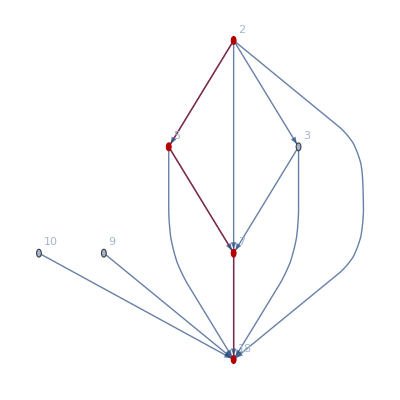
{{4,{2,5,7,18},-Graphics-}}

```mathematica
LongestIncreasingSequence[{10,9,2,5,3,7,18}]
```

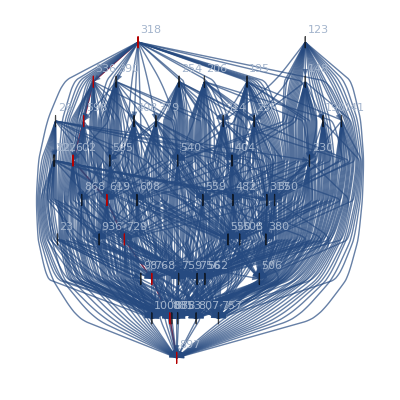
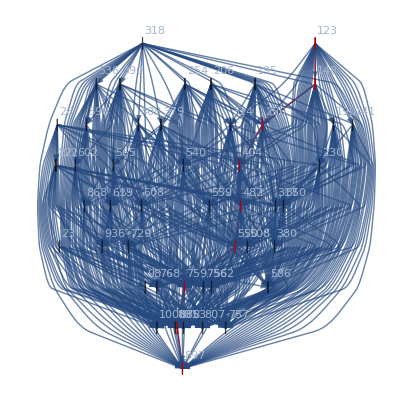
{{9,{318,536,598,602,619,729,768,881,897},-Graphics-},{9,{123,148,256,404,482,550,759,878,897},-Graphics-}}

```mathematica
LongestIncreasingSequence[FromDigits/@StringSplit["318   536   390   598   602   408   254   868   379   565
 206   619   936   195   123   314   729   608   148   540
 256   768   404   190   559   1000   482   141   26  230
 550   881   759   122   878  350  756  82  562  897  508
 853  317   380   807   23   506   98   757 ", Whitespace]]
```

```mathematica
list=FromDigits/@StringSplit["318   536   390   598   602   408   254   868   379   565
 206   619   936   195   123   314   729   608   148   540
 256   768   404   190   559   1000   482   141   26  230
 550   881   759   122   878  350  756  82  562  897  508
 853  317   380   807   23   506   98   757 ", Whitespace]
```

{318,536,390,598,602,408,254,868,379,565,206,619,936,195,123,314,729,608,148,540,256,768,404,190,559,1000,482,141,26,230,550,881,759,122,878,350,756,82,562,897,508,853,317,380,807,23,506,98,757}

```mathematica
Join[LongestCommonSequence[list, Sort[list]]]
```

{318,536,598,602,619,729,768,881,897}